# This .nb looks at the relation between z and d_l.

```mathematica
Clear[IS2, f, dl, c, Ho]
```

```mathematica
IS2[f_,a_,b_,n_]:=(h=(b-a)/3/n;3 h/8*Sum[(f[a+(3 i-3)*h]+3*f[a+(3 i-2)*h]+3 f[a+(3 i-1)*h]+f[a+(3 i)*h]),{i,1,n}]);
f[x_]:=1/Sqrt[0.308x+ 0.692 x^4];
```

```mathematica
dl[z_]:=c/Ho*(1+z)*IS2[f,(1+z)^-1,1,5];
```

```mathematica
c = 299792.458; Ho = 50
```

50

## Plot of dl over z from 0 to 100

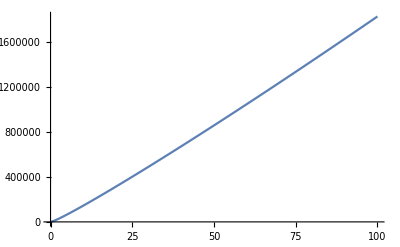

```mathematica
Plot[dl[z],{z, 0,100}]
```

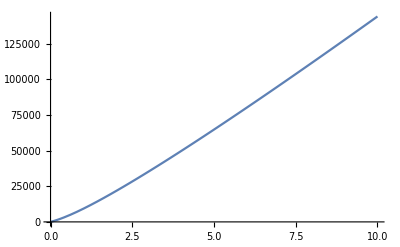

```mathematica
Plot[dl[z],{z, 0,10}]
```

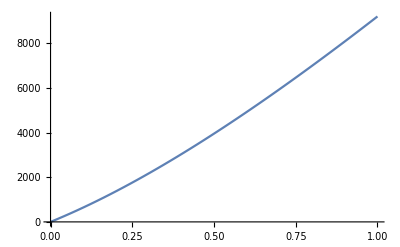

```mathematica
Plot[dl[z],{z, 0,1}]
```

## Log dl over z, from z = 0 to 100

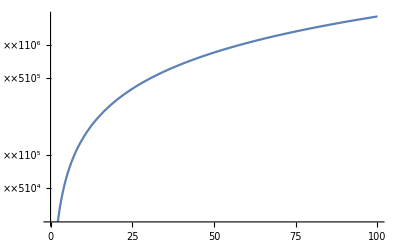

```mathematica
Plot[dl[z],{z, 0,100},ScalingFunctions->"Log10"]
```

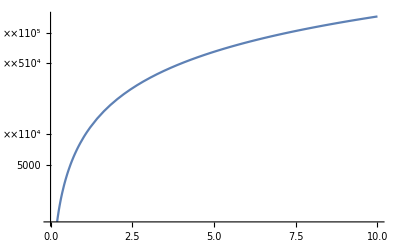

```mathematica
Plot[dl[z],{z, 0,10},ScalingFunctions->"Log10"]
```

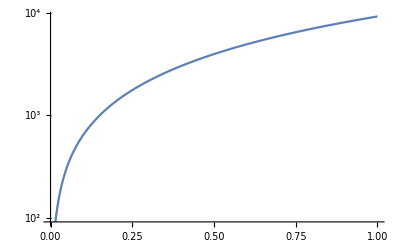

```mathematica
Plot[dl[z],{z, 0,1},ScalingFunctions->"Log10"]
```